```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
GeneratePsis[order_]:=Block[{sz,i,j,w,psis,temp,xi,eta},
sz=(2+order-1)(2+order-1);
psis=Table[0,{sz}];
temp=1;
For[i=1,i≤ 1+order,i++,
For[j=1,j≤ 1+order,j++,
psis[[temp]]=(ComputeShape[order,xi][[j]]ComputeShape[order,eta][[i]])*(1);
temp++;
];
];
psis
];
```

```mathematica
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta},
(*psis=GeneratePsis[order];*)
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
(*Print["J12 = ",Jac[[1,2]]];*)
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
Contribute[data_,weight_,order_]:=Block[{InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
{psi,GradPsi,Jac,x,y}=data;
(*Print["Jac= ",Jac//MatrixForm];
Print["GradPsi= ",GradPsi//MatrixForm];*)
InvJac=Inverse[Jac];

DetJ=Det[Jac];
(*Print["InvJac= ",InvJac//MatrixForm];*)
(*GradPhi=Table[InvJac .GradPsi[[i]],{i,1,Length[GradPsi]}];*)
(*Print["InvJac =",InvJac];
Print["Transpose[GradPsi] =",Transpose[GradPsi]];*)
GradPhi=InvJac.Transpose[GradPsi];
(*Print[GradPhi];*)
wpLocal=weight  DetJ;
nnodes=4 order;
ek=Table[0,{nnodes},{nnodes}];
ef=Table[0,{nnodes}];
For[i=1,i≤ nnodes,i++,
ef[[i]] +=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[i,j]]+=(GradPhi[[1,i]]  GradPhi[[1,j]]+GradPhi[[2,i]]  GradPhi[[2,j]])wpLocal;
];
];
(*Print["ek =",ek//MatrixForm];*)
{ek,ef}
]
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
nnodes=4 order ;
{psi,GradPsi,Jac,x,y}=data;
(*Print["Jac= ",Jac//MatrixForm];
Print["GradPsi= ",GradPsi//MatrixForm];*)
InvJac=Inverse[Jac];

DetJ=Det[Jac];
(*Print["DetJac = ",DetJ];*)
(*Print["InvJac= ",InvJac//MatrixForm];*)
(*GradPhi=Table[InvJac .GradPsi[[i]],{i,1,Length[GradPsi]}];*)
(*Print["InvJac =",InvJac];
Print["Transpose[GradPsi] =",Transpose[GradPsi]];*)
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
(*Print["C = ",C//MatrixForm];*)
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
fu=-1;
For[i=1,i≤ nnodes,i++,

(*Print["x = ",x];*)
ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
(*ef[[(2*i+fu)]]+=
ef[[(2*i+fu)]]+=
ef[[(2*i+1+fu)]]+=
ef[[(2*i+1+fu)]]+=*)
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];
(*Print["ek =",ek//MatrixForm];*)
{ek,ef}
]
```

```mathematica
CalcStiff[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes },{nnodes }];
ef=Table[0,{nnodes }];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=Contribute[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
coords={{2,1},{5,2},{4,6},{1,4}}
order=1;
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu))
{ek,ef}=CalcStiff[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{2,1},{5,2},{4,6},{1,4}}

5.76923×10^6

Ke = (0.649446 | -0.224565 | -0.250396 | -0.174486
-0.224565 | 0.747872 | -0.0889748 | -0.434333
-0.250396 | -0.0889748 | 0.535432 | -0.196061
-0.174486 | -0.434333 | -0.196061 | 0.804879)

Fe = (0.
0.
0.
0.)

```mathematica
coords={{0,0},{10,0},{10,6},{0,6}}
bc={{2,{6000,0}},{3,{6000,0}}}
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu))
{ek,ef}=CalcStiffElastic[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{0,0},{10,0},{10,6},{0,6}}

{{2,{6000,0}},{3,{6000,0}}}

5.76923×10^6

Ke = (4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

Fe = (0.
0.
0.
0.
0.
0.
0.
0.)

```mathematica
ek//MatrixForm
```

(4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

```mathematica
B={{dN1dx,0,dN2dx,0,dN3dx,0,dN4dx,0},{0,dN1dy,0,dN2dy,0,dN3dy,0,dN4dy},{dN1dy,dN1dx,dN2dy,dN2dx,dN3dy,dN3dx,dN4dy,dN4dx}}/.{dN1dx->-(b-y)/(a b),dN2dx->(b-y)/(a b),dN3dx->y/(a b),dN4dx->-y/(a b),dN1dy->-(a-x)/(a b),dN2dy->-x/(a b),dN3dy->x/(a b),dN4dy->(a-x)/(a b)};
c={{EE /(1-Nu^2),EE Nu/(1-Nu^2),0},{EE Nu/(1-Nu^2),EE /(1-Nu^2),0},{0,0,EE/(2(1+Nu))}}/.{EE->young,Nu->nu};
(*c={{C11,C12,0},{C12,C22,0},{0,0,C33}}*)
k=NIntegrate[Transpose[B].c.B/.{a->10,b->6},{x,0,10},{y,0,6}];
Chop[ek-k,10^-5]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
coords={{0,0},{5,0},{5,3},{0,3}}
bc={{2,{6000,0}},{3,{6000,0}}}
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu))
{ek,ef}=CalcStiffElastic[order,coords];
Print["Ke = ",ek//MatrixForm];
Print["Fe = ",ef//MatrixForm];
```

{{0,0},{5,0},{5,3},{0,3}}

{{2,{6000,0}},{3,{6000,0}}}

5.76923×10^6

Ke = (4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

Fe = (0.
0.
0.
0.
0.
0.
0.
0.)

```mathematica
CreateRectangularMesh[a_,b_,nx_,ny_]:=Block[{cols,rows,coords,i,j,deltax,deltay,co1,co2,co3,co4,elvec,xstart,ystart,temp},

cols=(nx+2);
rows=(ny+2);
coords=Table[0,{rows},{cols}];

deltax=(b[[1]]-a[[1]])/(nx+1);
deltay=(b[[2]]-a[[2]])/(ny+1);
xstart=a[[1]];
ystart=a[[2]];
temp={0,0};

For[i=1,i≤ rows,i++,
For[j=1,j≤cols,j++,
coords[[i,j]]={xstart,ystart};
xstart+=deltax;
];
ystart+=deltay;
xstart=a[[1]];
];

elvec={};
For[i=1,i<rows,i++,
For[j=1,j<cols,j++,
co1=coords[[i,j]];
co2=coords[[i,j+1]];
co3=coords[[i+1,j]];
co4=coords[[i+1,j+1]];
AppendTo[elvec,{co1,co2,co4 ,co3}];
];
];
elvec
]
```

2

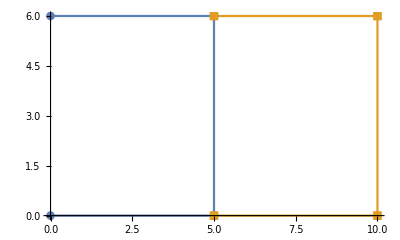

```mathematica
s=CreateRectangularMesh[{0,0},{10,6},1,0];
Length[s]
ListLinePlot[s,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
```

```mathematica
ComputeNNodes[RectangularMesh_]:=Block[{allnodes,i,j,alreadcomputednodes,node,newnode,nnodes,y0,nn,firstrow,resto},
allnodes=Flatten[RectangularMesh,1]//N;
y0=allnodes[[1,2]];
(*Print[allnodes];*)
alreadcomputednodes={};
For[i=1,i≤Length[allnodes],i++,
node=allnodes[[i]];
For[j=1+i,j<=Length[allnodes],j++,
If[node==allnodes[[j]], AppendTo[alreadcomputednodes,node]];
];
];
(*Print[alreadcomputednodes];*)
newnode=allnodes;
For[i=1,i<=Length[alreadcomputednodes],i++,
newnode=DeleteCases[newnode,alreadcomputednodes[[i]]];
AppendTo[newnode,alreadcomputednodes[[i]]];

];
nn=newnode;
firstrow={};
resto={};
For[i=1,i≤Length[nn],i++,
If[nn[[i,2]]==y0,
AppendTo[firstrow,nn[[i]]];
,
AppendTo[resto,nn[[i]]];
];
firstrow=SortBy[firstrow,Last];
resto=SortBy[resto,Last];
resto=Sort[resto,#1[[2]]<#2[[2]]&];
];
PrependTo[resto,firstrow];
ArrayReshape[resto,{Length[nn],2}]
];
```

```mathematica
ComputeTopol[allnodes_]:=Block[{s,ss,i,j,k,topol,topolvec,topolgeral},
topolvec={};
s=allnodes//N;
ss=ComputeNNodes[s]//N;
topolgeral={};
For[i=1,i≤Length[s],i++,

topol=Table[0,{4}];
For[j=1,j≤4,j++,
For[k=1,k≤Length[ss],k++,
If[s[[i,j]]==ss[[k]],
topol[[j]]=k;
AppendTo[topolgeral,k];
];
];

];
AppendTo[topolvec,topol];

];
topolvec
];
```

```mathematica
Assemble[allcoords_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co,nnodes,topol},

p=order;
nels=Length[allcoords];
nnodes=ComputeNNodes[allcoords]//N;
(*Print["Nnodes = ",nnodes];*)
sz=Length[nnodes] 2;
rows=order 4;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
(*Print["Kglob = ",Kglob//MatrixForm];*)
topol=ComputeTopol[allcoords];
Print["topol = ",topol];
For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
(*Print["k = ",k];*)
(*Print["co = ",co];*)
{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)

ik=(k-1)*order 4;
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];

];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
ApplyBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];

];
{kglob,fglob}
]
```

topol = {{1,2,3,4}}

8

KE = (4.33455×10^18 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^18 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^18 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^18 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

FE = (0
0
6000
0
6000.
0
0
0)

{6.92113×10^-12,-4.0383×10^-28,20.,2.01915×10^-28,20.,4.2,6.92113×10^-12,4.2}

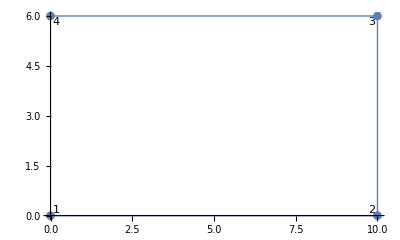

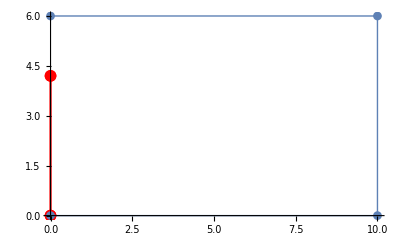

```mathematica
allcoords=CreateRectangularMesh[{0,0},{10,6},0,0];
nnodes=ComputeNNodes[allcoords]//N;
{KE,FE}=Assemble[allcoords,1,1];

(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyBC[KE,FE,4,0,{{10^12,1},{1,1}},{0,0}];

(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyBC[KE,FE,2,1,{{1,1},{1,1}},{6000,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyBC[KE,FE,3,1,{{1,1},{1,1}},{6000,0}];



Length[KE]
Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=5000;
deformed=(Flatten[nnodes]+scale sol)

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];


nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

topol = {{1,2,9,10},{2,3,8,9},{3,4,7,8},{4,5,6,7},{10,9,14,15},{9,8,13,14},{8,7,12,13},{7,6,11,12}}

30

KE = (1.48352×10^7 | 5.35714×10^6 | -9.06593×10^6 | -412088. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 1.64835×10^6 | 412088. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5.35714×10^6 | 1.48352×10^19 | 412088. | 1.64835×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | -412088. | -9.06593×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-9.06593×10^6 | 412088. | 2.96703×10^7 | 0. | -9.06593×10^6 | -412088. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-412088. | 1.64835×10^6 | 0. | 2.96703×10^19 | 412088. | 1.64835×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | 5.82077×10^-11 | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -9.06593×10^6 | 412088. | 2.96703×10^7 | 0. | -9.06593×10^6 | -412088. | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -412088. | 1.64835×10^6 | 0. | 2.96703×10^19 | 412088. | 1.64835×10^6 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | 5.82077×10^-11 | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -9.06593×10^6 | 412088. | 2.96703×10^7 | 0. | -9.06593×10^6 | -412088. | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -412088. | 1.64835×10^6 | 0. | 2.96703×10^19 | 412088. | 1.64835×10^6 | -5.35714×10^6 | -7.41758×10^6 | 5.82077×10^-11 | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -9.06593×10^6 | 412088. | 1.48352×10^19 | -5.35714×10^6 | 1.64835×10^6 | -412088. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -412088. | 1.64835×10^6 | -5.35714×10^6 | 1.48352×10^19 | 412088. | -9.06593×10^6 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 1.64835×10^6 | 412088. | 2.96703×10^19 | 0. | -1.81319×10^7 | 5.82077×10^-11 | 0 | 0 | 0 | 0 | 0 | 0 | 1.64835×10^6 | -412088. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | -412088. | -9.06593×10^6 | 0. | 2.96703×10^7 | 0. | 3.2967×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 412088. | -9.06593×10^6 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | -1.81319×10^7 | 0. | 5.93407×10^7 | 0. | -1.81319×10^7 | 5.82077×10^-11 | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | 0. | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0. | 3.2967×10^6 | 0. | 5.93407×10^7 | 0. | 3.2967×10^6 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | 5.82077×10^-11 | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0
0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | -1.81319×10^7 | 0. | 5.93407×10^7 | 0. | -1.81319×10^7 | 5.82077×10^-11 | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0
0 | 0 | -5.35714×10^6 | -7.41758×10^6 | 0. | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0. | 3.2967×10^6 | 0. | 5.93407×10^7 | 0. | 3.2967×10^6 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | 5.82077×10^-11 | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0
-7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.81319×10^7 | 0. | 5.93407×10^7 | 0. | -1.81319×10^7 | 5.82077×10^-11 | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | 5.35714×10^6
-5.35714×10^6 | -7.41758×10^6 | 0. | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 3.2967×10^6 | 0. | 5.93407×10^7 | 0. | 3.2967×10^6 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | 5.82077×10^-11 | -1.81319×10^7 | 5.35714×10^6 | -7.41758×10^6
1.64835×10^6 | -412088. | -7.41758×10^6 | 5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.81319×10^7 | 0. | 2.96703×10^7 | 0. | 0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | -5.35714×10^6 | 1.64835×10^6 | 412088.
412088. | -9.06593×10^6 | 5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0. | 3.2967×10^6 | 0. | 2.96703×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | -5.35714×10^6 | -7.41758×10^6 | -412088. | -9.06593×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.64835×10^6 | 412088. | -7.41758×10^6 | -5.35714×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 1.48352×10^19 | 5.35714×10^6 | -9.06593×10^6 | -412088. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -412088. | -9.06593×10^6 | -5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 5.35714×10^6 | 1.48352×10^7 | 412088. | 1.64835×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | 5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | -5.35714×10^6 | 0 | 0 | 0 | 0 | -9.06593×10^6 | 412088. | 2.96703×10^7 | 0. | -9.06593×10^6 | -412088. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.35714×10^6 | -7.41758×10^6 | 0. | -1.81319×10^7 | -5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | -412088. | 1.64835×10^6 | 0. | 2.96703×10^7 | 412088. | 1.64835×10^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | 5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | -5.35714×10^6 | 0 | 0 | 0 | 0 | -9.06593×10^6 | 412088. | 2.96703×10^7 | 0. | -9.06593×10^6 | -412088. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.35714×10^6 | -7.41758×10^6 | 0. | -1.81319×10^7 | -5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | -412088. | 1.64835×10^6 | 0. | 2.96703×10^7 | 412088. | 1.64835×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | 5.35714×10^6 | 3.2967×10^6 | 0. | -7.41758×10^6 | -5.35714×10^6 | 0 | 0 | 0 | 0 | -9.06593×10^6 | 412088. | 2.96703×10^7 | 0. | -9.06593×10^6 | -412088.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.35714×10^6 | -7.41758×10^6 | 0. | -1.81319×10^7 | -5.35714×10^6 | -7.41758×10^6 | 0 | 0 | 0 | 0 | -412088. | 1.64835×10^6 | 0. | 2.96703×10^7 | 412088. | 1.64835×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.41758×10^6 | 5.35714×10^6 | 1.64835×10^6 | -412088. | 0 | 0 | 0 | 0 | 0 | 0 | -9.06593×10^6 | 412088. | 1.48352×10^7 | -5.35714×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.35714×10^6 | -7.41758×10^6 | 412088. | -9.06593×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -412088. | 1.64835×10^6 | -5.35714×10^6 | 1.48352×10^7)

FE = (0
0
0
0
0
0
0
0
0
0
0
0
0.
0
0.
0
0.
0
0.
0
0
97.463
0.
179.987
0.
137.833
0.
74.594
0.
12.756)

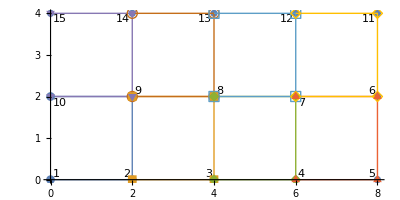

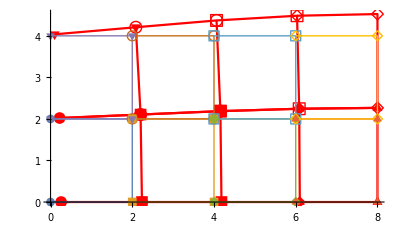

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

allcoords=CreateRectangularMesh[{0,0},{8,4},3,1];
nnodes=ComputeNNodes[allcoords]//N;
{KE,FE}=Assemble[allcoords,1,1];


(*Dirichlet - vy=0 vy=0 no no 1*)
{KE,FE}=ApplyBC[KE,FE,1,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - vy=0 no no 3*)
{KE,FE}=ApplyBC[KE,FE,3,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - vy=0 no no 4*)
{KE,FE}=ApplyBC[KE,FE,4,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - ux=0 e vy=0 no no 5*)
{KE,FE}=ApplyBC[KE,FE,5,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet - ux=0 no no 6*)
{KE,FE}=ApplyBC[KE,FE,6,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 11*)
{KE,FE}=ApplyBC[KE,FE,11,0,{{10^12,1},{1,1}},{0,0}];

(*Newman - fy=97463 no no 11*)
{KE,FE}=ApplyBC[KE,FE,11,1,{{1,1},{1,1}},{0,97.463}];

(*Newman - fy=179987 no no 12*)
{KE,FE}=ApplyBC[KE,FE,12,1,{{1,1},{1,1}},{0,179.987}];

(*Newman - fy=137833 no no 13*)
{KE,FE}=ApplyBC[KE,FE,13,1,{{1,1},{1,1}},{0,137.833}];

(*Newman - fy=74594 no no 14*)
{KE,FE}=ApplyBC[KE,FE,14,1,{{1,1},{1,1}},{0,74.594}];

(*Newman - fy=12756 no no 15*)
{KE,FE}=ApplyBC[KE,FE,15,1,{{1,1},{1,1}},{0,12.756 }];



Length[KE]
Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];


nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

{{{2,1},{5,2},{4,6},{1,4}}}

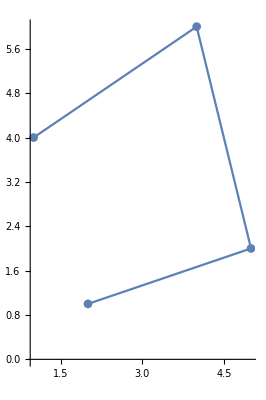

topol = {{1,2,4,3}}

KE = (0.407005 | 0.104972 | -0.300742 | -0.139621 | -0.0160288 | 0.150145 | -0.0902343 | -0.115496
0.104972 | 0.545515 | -0.0729543 | -0.0286192 | 0.0834783 | -0.239883 | -0.115496 | -0.277013
-0.300742 | -0.0729543 | 0.702964 | -0.142679 | -0.454073 | 0.13441 | 0.0518507 | 0.0812231
-0.139621 | -0.0286192 | -0.142679 | 0.393915 | 0.13441 | -0.182949 | 0.14789 | -0.182347
-0.0160288 | 0.0834783 | -0.454073 | 0.13441 | 0.748217 | -0.144182 | -0.278116 | -0.073706
0.150145 | -0.239883 | 0.13441 | -0.182949 | -0.144182 | 0.432273 | -0.140373 | -0.00944048
-0.0902343 | -0.115496 | 0.0518507 | 0.14789 | -0.278116 | -0.140373 | 0.316499 | 0.107979
-0.115496 | -0.277013 | 0.0812231 | -0.182347 | -0.073706 | -0.00944048 | 0.107979 | 0.4688)

FE = (0.
0
0.
0
0.
0
0.
0)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}}
undefplot=ListLinePlot[allcoords,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
{KE,FE}=Assemble[allcoords,1,1];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

```mathematica
Integrate[Cos[x y]2,{x,0,4},{y,0,4.}]
```

3.2626

-Graphics3D-

topol = {{1,2,21,22},{2,3,20,21},{3,4,19,20},{4,5,18,19},{5,6,17,18},{6,7,16,17},{7,8,15,16},{8,9,14,15},{9,10,13,14},{10,11,12,13},{22,21,32,33},{21,20,31,32},{20,19,30,31},{19,18,29,30},{18,17,28,29},{17,16,27,28},{16,15,26,27},{15,14,25,26},{14,13,24,25},{13,12,23,24},{33,32,43,44},{32,31,42,43},{31,30,41,42},{30,29,40,41},{29,28,39,40},{28,27,38,39},{27,26,37,38},{26,25,36,37},{25,24,35,36},{24,23,34,35},{44,43,54,55},{43,42,53,54},{42,41,52,53},{41,40,51,52},{40,39,50,51},{39,38,49,50},{38,37,48,49},{37,36,47,48},{36,35,46,47},{35,34,45,46},{55,54,65,66},{54,53,64,65},{53,52,63,64},{52,51,62,63},{51,50,61,62},{50,49,60,61},{49,48,59,60},{48,47,58,59},{47,46,57,58},{46,45,56,57},{66,65,76,77},{65,64,75,76},{64,63,74,75},{63,62,73,74},{62,61,72,73},{61,60,71,72},{60,59,70,71},{59,58,69,70},{58,57,68,69},{57,56,67,68},{77,76,87,88},{76,75,86,87},{75,74,85,86},{74,73,84,85},{73,72,83,84},{72,71,82,83},{71,70,81,82},{70,69,80,81},{69,68,79,80},{68,67,78,79},{88,87,98,99},{87,86,97,98},{86,85,96,97},{85,84,95,96},{84,83,94,95},{83,82,93,94},{82,81,92,93},{81,80,91,92},{80,79,90,91},{79,78,89,90},{99,98,109,110},{98,97,108,109},{97,96,107,108},{96,95,106,107},{95,94,105,106},{94,93,104,105},{93,92,103,104},{92,91,102,103},{91,90,101,102},{90,89,100,101},{110,109,120,121},{109,108,119,120},{108,107,118,119},{107,106,117,118},{106,105,116,117},{105,104,115,116},{104,103,114,115},{103,102,113,114},{102,101,112,113},{101,100,111,112}}

242

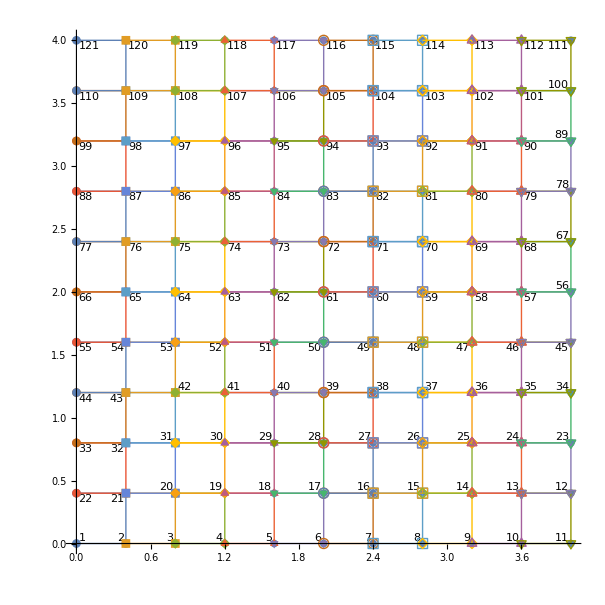

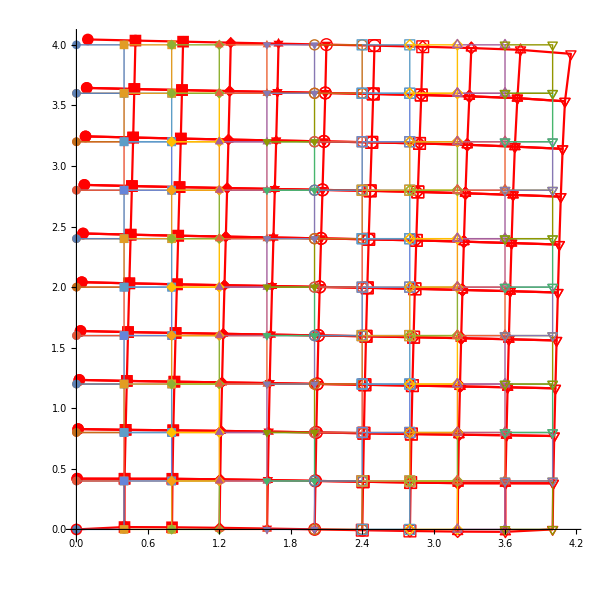

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
Forcing[x_,y_]:=Block[{},
(*10(4-x)(0-x)(4-y)(0-y)*)
0
]
Plot3D[Forcing[x,y],{x,0,4},{y,0,4}]

allcoords=CreateRectangularMesh[{0,0},{4,4},9,9];
undefplot=ListLinePlot[allcoords,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True];
nnodes=ComputeNNodes[allcoords]//N;
{KE,FE}=Assemble[allcoords,1,1];

(*Dirichlet - vy=0 vy=0 no no 1*)
{KE,FE}=ApplyBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyBC[KE,FE,11,0,{{10^12,1},{1,10^12}},{0,0}];
(*Newman - fy=12756 no no 15*)
{KE,FE}=ApplyBC[KE,FE,111,1,{{1,1},{1,1}},{10000,0}];

Length[KE]
(*Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]*)

sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=30;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];


nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
nnodes[[11]]
nnodes[[34]]
```

{4.,0.}

{4.,1.2}

```mathematica
a=nnodes[[1]];
b=nnodes[[6]];

DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
nnodes
```

{{0.,0.},{0.4,0.},{0.8,0.},{1.2,0.},{1.6,0.},{2.,0.},{2.4,0.},{2.8,0.},{3.2,0.},{3.6,0.},{4.,0.},{4.,0.4},{3.6,0.4},{3.2,0.4},{2.8,0.4},{2.4,0.4},{2.,0.4},{1.6,0.4},{1.2,0.4},{0.8,0.4},{0.4,0.4},{0.,0.4},{4.,0.8},{3.6,0.8},{3.2,0.8},{2.8,0.8},{2.4,0.8},{2.,0.8},{1.6,0.8},{1.2,0.8},{0.8,0.8},{0.4,0.8},{0.,0.8},{4.,1.2},{3.6,1.2},{3.2,1.2},{2.8,1.2},{2.4,1.2},{2.,1.2},{1.6,1.2},{1.2,1.2},{0.8,1.2},{0.4,1.2},{0.,1.2},{4.,1.6},{3.6,1.6},{3.2,1.6},{2.8,1.6},{2.4,1.6},{2.,1.6},{1.6,1.6},{1.2,1.6},{0.8,1.6},{0.4,1.6},{0.,1.6},{4.,2.},{3.6,2.},{3.2,2.},{2.8,2.},{2.4,2.},{2.,2.},{1.6,2.},{1.2,2.},{0.8,2.},{0.4,2.},{0.,2.},{4.,2.4},{3.6,2.4},{3.2,2.4},{2.8,2.4},{2.4,2.4},{2.,2.4},{1.6,2.4},{1.2,2.4},{0.8,2.4},{0.4,2.4},{0.,2.4},{4.,2.8},{3.6,2.8},{3.2,2.8},{2.8,2.8},{2.4,2.8},{2.,2.8},{1.6,2.8},{1.2,2.8},{0.8,2.8},{0.4,2.8},{0.,2.8},{4.,3.2},{3.6,3.2},{3.2,3.2},{2.8,3.2},{2.4,3.2},{2.,3.2},{1.6,3.2},{1.2,3.2},{0.8,3.2},{0.4,3.2},{0.,3.2},{4.,3.6},{3.6,3.6},{3.2,3.6},{2.8,3.6},{2.4,3.6},{2.,3.6},{1.6,3.6},{1.2,3.6},{0.8,3.6},{0.4,3.6},{0.,3.6},{4.,4.},{3.6,4.},{3.2,4.},{2.8,4.},{2.4,4.},{2.,4.},{1.6,4.},{1.2,4.},{0.8,4.},{0.4,4.},{0.,4.}}

```mathematica
{els,ids}=DefineLineNodes[5,11,nnodes]
```

{{{{1.6,0.},{2.,0.}},{{2.,0.},{2.4,0.}},{{2.4,0.},{2.8,0.}},{{2.8,0.},{3.2,0.}},{{3.2,0.},{3.6,0.}},{{3.6,0.},{4.,0.}}},{5,6,7,8,9,10,11}}

```mathematica
Clear[nodes]
ComputeNewLinearNodes[order_,coords_]:=Block[{xa,xb,newcoords},
xa=coords[[1]];
xb=coords[[2]];
newcoords=Table[xa+(1-i)(xa-xb)/order,{i,1,order+1}];
newcoords
]
```

```mathematica
ContributeLine[EK_,EF_,fx_,order_,nodes_,id1_,id2_]:=Block[{els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco},


{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co={els[[i]][[1,1]],els[[i]][[2,1]]};
newco=ComputeNewLinearNodes[order,co];
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]])/.xi->xix[[i]]) w[[i]]J,{i,1,Length[xix]}],{j,1,Length[shapes]}];
Print["Fi = ",integralxi1];
];

]
```

```mathematica
(*nodes={{0,0},{1,0},{2,0},{3,0}};
f[x_]:=3x-x x;
ContributeLine[KE,FE,f,1,nodes,1,4]*)
```

```mathematica
q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
ContributeLine[KE,FE,f,1,nnodes,15,11]
```

```mathematica
ContributeLineNewman[EF_,fx_,order_,nodes_,id1_,id2_,fxorfy_]:=Block[{Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];

If[fxorfy==1,(*fy*)
co={els[[i]][[1,1]],els[[i]][[2,1]]};
Print["co = ",co];
,
(*fx*)
co={els[[i]][[1,2]],els[[i]][[2,2]]};
];

newco=ComputeNewLinearNodes[order,co];
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]])/.xi->xix[[i]]) w[[i]]J,{i,1,Length[xix]}],{j,1,Length[shapes]}];
Print["ids[[i]] = ",ids[[i]]];
If[fxorfy==1,(*fy*)
Ef[[ ids[[i]] 2]]+=integralxi1[[1]];
Ef[[ ids[[i+1]] 2]]+=integralxi1[[2]];
,
(*fx*)
Ef[[ ids[[i]] ]]+=integralxi1[[1]];
Ef[[ ids[[i+1]] ]]+=integralxi1[[2]];
];
];
Ef
];
```

```mathematica
ApplyBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];

];
{kglob,fglob}
]
```

```mathematica
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

topol = {{1,2,9,10},{2,3,8,9},{3,4,7,8},{4,5,6,7},{10,9,14,15},{9,8,13,14},{8,7,12,13},{7,6,11,12}}

co = {8.,6.}

ids[[i]] = 11

co = {6.,4.}

ids[[i]] = 12

co = {4.,2.}

ids[[i]] = 13

co = {2.,0.}

ids[[i]] = 14

-Graphics-

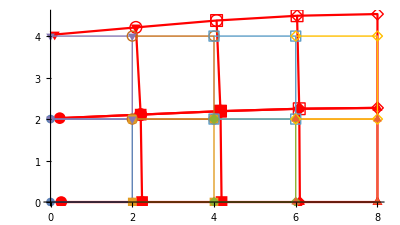

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords=CreateRectangularMesh[{0,0},{8,4},3,1];

nnodes=ComputeNNodes[allcoords]//N;
{KE,FE}=Assemble[allcoords,1,1];
newkt=KE;
KEt=KE;

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,5,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,5,11,{{10^12,1},{1,1}},{0,0}];


q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,1,nnodes,15,11,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
sol[[2 15]]
sol[[2 15-1]]
```

9.32296×10^-7

2.5422×10^-6

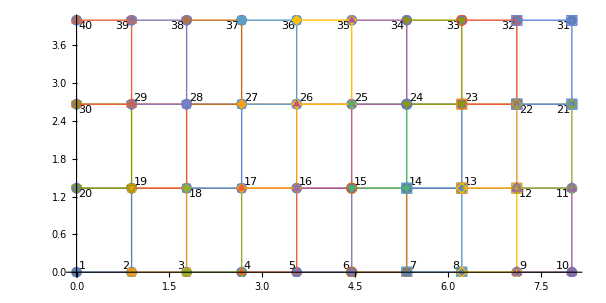

```mathematica
allcoords=CreateRectangularMesh[{0,0},{8,4},8,2];
nnodes=ComputeNNodes[allcoords]//N;
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
```

topol = {{1,2,19,20},{2,3,18,19},{3,4,17,18},{4,5,16,17},{5,6,15,16},{6,7,14,15},{7,8,13,14},{8,9,12,13},{9,10,11,12},{20,19,29,30},{19,18,28,29},{18,17,27,28},{17,16,26,27},{16,15,25,26},{15,14,24,25},{14,13,23,24},{13,12,22,23},{12,11,21,22},{30,29,39,40},{29,28,38,39},{28,27,37,38},{27,26,36,37},{26,25,35,36},{25,24,34,35},{24,23,33,34},{23,22,32,33},{22,21,31,32}}

co = {8.,7.11111}

ids[[i]] = 31

co = {7.11111,6.22222}

ids[[i]] = 32

co = {6.22222,5.33333}

ids[[i]] = 33

co = {5.33333,4.44444}

ids[[i]] = 34

co = {4.44444,3.55556}

ids[[i]] = 35

co = {3.55556,2.66667}

ids[[i]] = 36

co = {2.66667,1.77778}

ids[[i]] = 37

co = {1.77778,0.888889}

ids[[i]] = 38

co = {0.888889,0.}

ids[[i]] = 39

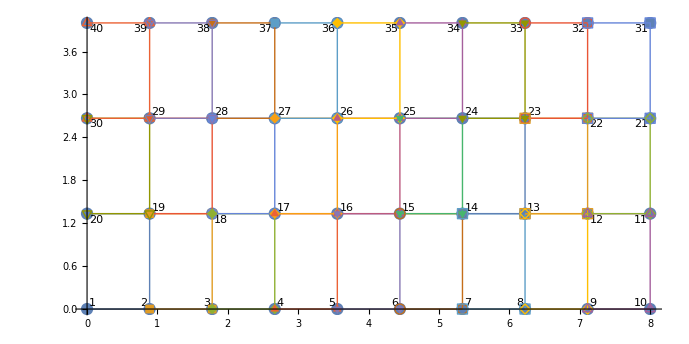

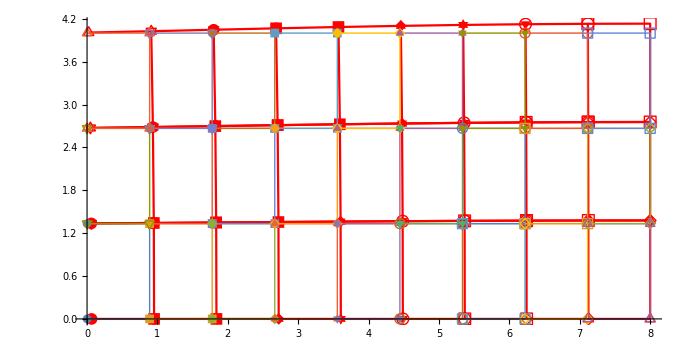

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

{KE,FE}=Assemble[allcoords,1,1];
newkt=KE;
KEt=KE;

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,10,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,10,31,{{10^12,1},{1,1}},{0,0}];


q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,1,nnodes,40,31,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=10000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
sol[[40 2]]
sol[[40 2-1]]
```

7.33573×10^-7

2.40043×10^-6

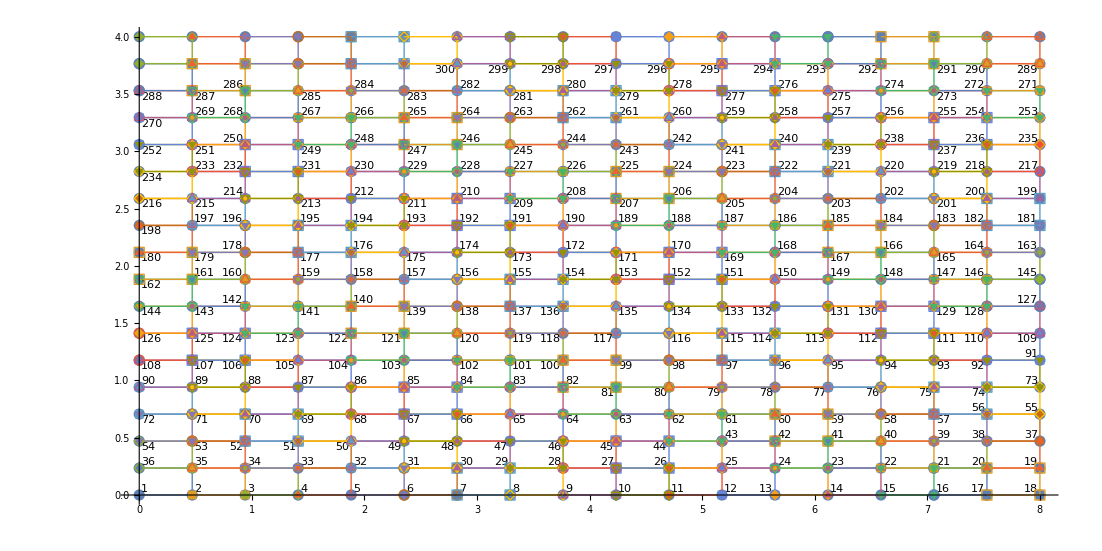

```mathematica
allcoords=CreateRectangularMesh[{0,0},{8,4},16,16];
nnodes=ComputeNNodes[allcoords]//N;
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
```

topol = {{1,2,35,36},{2,3,34,35},{3,4,33,34},{4,5,32,33},{5,6,31,32},{6,7,30,31},{7,8,29,30},{8,9,28,29},{9,10,27,28},{10,11,26,27},{11,12,25,26},{12,13,24,25},{13,14,23,24},{14,15,22,23},{15,16,21,22},{16,17,20,21},{17,18,19,20},{36,35,53,54},{35,34,52,53},{34,33,51,52},{33,32,50,51},{32,31,49,50},{31,30,48,49},{30,29,47,48},{29,28,46,47},{28,27,45,46},{27,26,44,45},{26,25,43,44},{25,24,42,43},{24,23,41,42},{23,22,40,41},{22,21,39,40},{21,20,38,39},{20,19,37,38},{54,53,71,72},{53,52,70,71},{52,51,69,70},{51,50,68,69},{50,49,67,68},{49,48,66,67},{48,47,65,66},{47,46,64,65},{46,45,63,64},{45,44,62,63},{44,43,61,62},{43,42,60,61},{42,41,59,60},{41,40,58,59},{40,39,57,58},{39,38,56,57},{38,37,55,56},{72,71,89,90},{71,70,88,89},{70,69,87,88},{69,68,86,87},{68,67,85,86},{67,66,84,85},{66,65,83,84},{65,64,82,83},{64,63,81,82},{63,62,80,81},{62,61,79,80},{61,60,78,79},{60,59,77,78},{59,58,76,77},{58,57,75,76},{57,56,74,75},{56,55,73,74},{90,89,107,108},{89,88,106,107},{88,87,105,106},{87,86,104,105},{86,85,103,104},{85,84,102,103},{84,83,101,102},{83,82,100,101},{82,81,99,100},{81,80,98,99},{80,79,97,98},{79,78,96,97},{78,77,95,96},{77,76,94,95},{76,75,93,94},{75,74,92,93},{74,73,91,92},{108,107,125,126},{107,106,124,125},{106,105,123,124},{105,104,122,123},{104,103,121,122},{103,102,120,121},{102,101,119,120},{101,100,118,119},{100,99,117,118},{99,98,116,117},{98,97,115,116},{97,96,114,115},{96,95,113,114},{95,94,112,113},{94,93,111,112},{93,92,110,111},{92,91,109,110},{126,125,143,144},{125,124,142,143},{124,123,141,142},{123,122,140,141},{122,121,139,140},{121,120,138,139},{120,119,137,138},{119,118,136,137},{118,117,135,136},{117,116,134,135},{116,115,133,134},{115,114,132,133},{114,113,131,132},{113,112,130,131},{112,111,129,130},{111,110,128,129},{110,109,127,128},{144,143,161,162},{143,142,160,161},{142,141,159,160},{141,140,158,159},{140,139,157,158},{139,138,156,157},{138,137,155,156},{137,136,154,155},{136,135,153,154},{135,134,152,153},{134,133,151,152},{133,132,150,151},{132,131,149,150},{131,130,148,149},{130,129,147,148},{129,128,146,147},{128,127,145,146},{162,161,179,180},{161,160,178,179},{160,159,177,178},{159,158,176,177},{158,157,175,176},{157,156,174,175},{156,155,173,174},{155,154,172,173},{154,153,171,172},{153,152,170,171},{152,151,169,170},{151,150,168,169},{150,149,167,168},{149,148,166,167},{148,147,165,166},{147,146,164,165},{146,145,163,164},{180,179,197,198},{179,178,196,197},{178,177,195,196},{177,176,194,195},{176,175,193,194},{175,174,192,193},{174,173,191,192},{173,172,190,191},{172,171,189,190},{171,170,188,189},{170,169,187,188},{169,168,186,187},{168,167,185,186},{167,166,184,185},{166,165,183,184},{165,164,182,183},{164,163,181,182},{198,197,215,216},{197,196,214,215},{196,195,213,214},{195,194,212,213},{194,193,211,212},{193,192,210,211},{192,191,209,210},{191,190,208,209},{190,189,207,208},{189,188,206,207},{188,187,205,206},{187,186,204,205},{186,185,203,204},{185,184,202,203},{184,183,201,202},{183,182,200,201},{182,181,199,200},{216,215,233,234},{215,214,232,233},{214,213,231,232},{213,212,230,231},{212,211,229,230},{211,210,228,229},{210,209,227,228},{209,208,226,227},{208,207,225,226},{207,206,224,225},{206,205,223,224},{205,204,222,223},{204,203,221,222},{203,202,220,221},{202,201,219,220},{201,200,218,219},{200,199,217,218},{234,233,251,252},{233,232,250,251},{232,231,249,250},{231,230,248,249},{230,229,247,248},{229,228,246,247},{228,227,245,246},{227,226,244,245},{226,225,243,244},{225,224,242,243},{224,223,241,242},{223,222,240,241},{222,221,239,240},{221,220,238,239},{220,219,237,238},{219,218,236,237},{218,217,235,236},{252,251,269,270},{251,250,268,269},{250,249,267,268},{249,248,266,267},{248,247,265,266},{247,246,264,265},{246,245,263,264},{245,244,262,263},{244,243,261,262},{243,242,260,261},{242,241,259,260},{241,240,258,259},{240,239,257,258},{239,238,256,257},{238,237,255,256},{237,236,254,255},{236,235,253,254},{270,269,287,288},{269,268,286,287},{268,267,285,286},{267,266,284,285},{266,265,283,284},{265,264,282,283},{264,263,281,282},{263,262,280,281},{262,261,279,280},{261,260,278,279},{260,259,277,278},{259,258,276,277},{258,257,275,276},{257,256,274,275},{256,255,273,274},{255,254,272,273},{254,253,271,272},{288,287,305,306},{287,286,304,305},{286,285,303,304},{285,284,302,303},{284,283,301,302},{283,282,300,301},{282,281,299,300},{281,280,298,299},{280,279,297,298},{279,278,296,297},{278,277,295,296},{277,276,294,295},{276,275,293,294},{275,274,292,293},{274,273,291,292},{273,272,290,291},{272,271,289,290},{306,305,323,324},{305,304,322,323},{304,303,321,322},{303,302,320,321},{302,301,319,320},{301,300,318,319},{300,299,317,318},{299,298,316,317},{298,297,315,316},{297,296,314,315},{296,295,313,314},{295,294,312,313},{294,293,311,312},{293,292,310,311},{292,291,309,310},{291,290,308,309},{290,289,307,308}}

co = {8.,7.52941}

ids[[i]] = 307

co = {7.52941,7.05882}

ids[[i]] = 308

co = {7.05882,6.58824}

ids[[i]] = 309

co = {6.58824,6.11765}

ids[[i]] = 310

co = {6.11765,5.64706}

ids[[i]] = 311

co = {5.64706,5.17647}

ids[[i]] = 312

co = {5.17647,4.70588}

ids[[i]] = 313

co = {4.70588,4.23529}

ids[[i]] = 314

co = {4.23529,3.76471}

ids[[i]] = 315

co = {3.76471,3.29412}

ids[[i]] = 316

co = {3.29412,2.82353}

ids[[i]] = 317

co = {2.82353,2.35294}

ids[[i]] = 318

co = {2.35294,1.88235}

ids[[i]] = 319

co = {1.88235,1.41176}

ids[[i]] = 320

co = {1.41176,0.941176}

ids[[i]] = 321

co = {0.941176,0.470588}

ids[[i]] = 322

co = {0.470588,0.}

ids[[i]] = 323

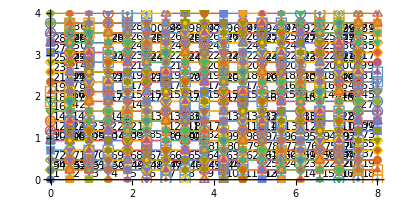

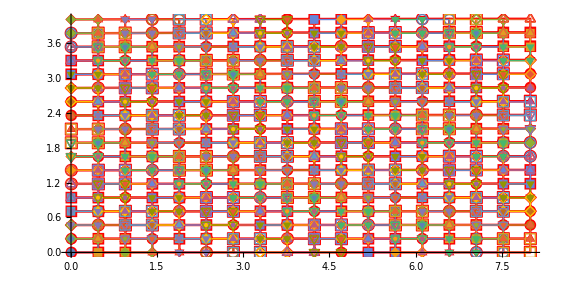

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

{KE,FE}=Assemble[allcoords,1,1];
newkt=KE;
KEt=KE;

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,18,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,18,307,{{10^12,1},{1,1}},{0,0}];


q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,1,nnodes,324,307,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=1000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
sol[[2 324-1]]
sol[[2 324]]
```

2.23871×10^-6

5.30213×10^-7

```mathematica
ComputeTopol[allnodes]
```

```mathematica
ComputeSol[els_,order_,alpha_,coords_]:=Block[{nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x,psis},
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};

For[i=1,i≤nels,i++,

For[j=1,j≤4,j++,
sol[[i]]+=(psis[[j]] alpha[[j+k]]);
(*Print["j+k = ",j+k];
Print["j = ",j];*)
];
k+=phisz-1;
];
{sol,dsol}
]
```